## Notebook Stochastic Simulation: Integrating the Mandelbrot set. Jeroen Hofman, student #: 10194754

```mathematica
SetDirectory[NotebookDirectory[]];
```

## Graphics

The operations below plot the array outputted by graphics.cpp to produce the mandelbrot set.

```mathematica
Image[Import["/home/jhofman/Desktop/SS/Project1/graphics.dat","Table"],ImageSize->500]
```

-Graphics-

## Analysis of results

Note: ErrorBarLogPlots is not a standard package, but it is used for plotting list plots with error on a log scale. Without this package the picture in the second routine below can not be rendered.

```mathematica
Needs["ErrorBarPlots`"];
Needs["ErrorBarLogPlots`"];
```

### Obtaining asymptote values by fitting with NonLinearModelFit

This routine fits for the 3 different sample methods and gives the fit result, it also shows a graphical example of the fit. By changing the input file to N_10E4_10.dat or N_10E5_10.dat the other sample sizes can be fitted as well. The results are collected (manually) in the routine below this one.

{{1.50669,0.000623669,2415.85,1.43524899931577×10^-4933},{0.00182767,0.00735176,0.248602,0.803685},{-0.000267739,0.000870372,-0.307614,0.758397}}

{{1.50681,0.000598619,2517.14,5.07849910670601×10^-4987},{0.00152415,0.00330717,0.460861,0.644932},{-0.00022122,0.000561217,-0.394179,0.693477}}

{{1.50673,0.0000805877,18696.7,1.49698869019329×10^-7597},{0.00135355,0.000276603,4.89349,1.04299×10^-6},{-0.000196612,0.0000615516,-3.19426,0.00141643}}

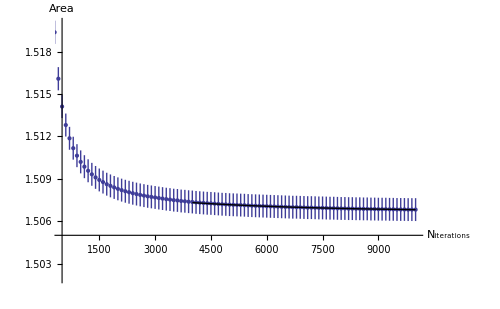

```mathematica
DataList = ReadList["N_10E6_10.dat",{Number,Number,Number}];
RSList = Drop[DataList,-20002];
LHList = Drop[Drop[DataList,10001],-10001];
ORList = Drop[DataList,20002];

RS = Drop[RSList,None,{3}];
RSError = Flatten[Drop[RSList,None,{1,2}]];

LH = Drop[LHList,None,{3}];
LHError = Flatten[Drop[LHList,None,{1,2}]];

OR = Drop[ORList,None,{3}];
ORError = Flatten[Drop[ORList,None,{1,2}]];

FitRS=NonlinearModelFit[Drop[RS,7000],c +a Exp[b  x],{{c,1.5},{a,0.001},{b,-0.001}},x,Weights->1/Drop[RSError,7000]^2,VarianceEstimatorFunction->(1 &),ConfidenceLevel->.99];
 FitRS["ParameterTableEntries"]

FitLH=NonlinearModelFit[Drop[LH,7000],c +a Exp[b  x],{{c,1.5},{a,0.001},{b,-0.001}},x,Weights->1/Drop[LHError,7000]^2,VarianceEstimatorFunction->(1 &),ConfidenceLevel->.99];
 FitLH["ParameterTableEntries"]

FitOR=NonlinearModelFit[Drop[OR,7000],c +a Exp[b  x],{{c,1.5},{a,0.001},{b,-0.001}},x,Weights->1/Drop[ORError,7000]^2,VarianceEstimatorFunction->(1 &),ConfidenceLevel->.99];
 FitOR["ParameterTableEntries"]

For[i=0, i<10000+1, i++,If[Mod[i,100]==0,RSList[[i/100 + 1]]=RSList[[i+1]]]];
RSPlot =Drop[ Drop[RSList,-(10000-10000/100)],None,{3}];
RSErrorPlot =Flatten[ Drop[Drop[RSList,-(10000-10000/100)],None,{1,2}]];

Show[ErrorListPlot[Join[RSPlot,Partition[RSErrorPlot,1],2]],Plot[FitRS[x],{x,4000,10000},PlotStyle->Directive[Thick,Black]],PlotRange->{{500,10000},{1.502,1.520}},AxesLabel->{"N_iterations","Area"},AxesOrigin->{500,1.505},ImageSize->500]
```

### Plotting asymptote values with errors obtained from routine above

By repeating the above for multiple input files with different sample sizes one can get fitting results for each of them. They are collected below and plotted to give an overview of the asymptote values.

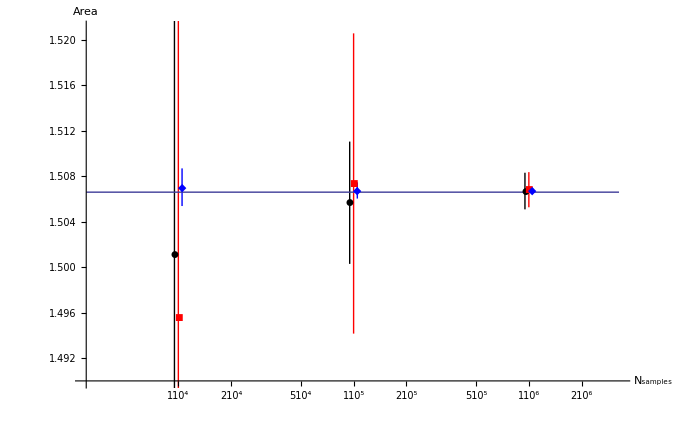

```mathematica
RSList10 = {{0.95*10^4,1.5010824964391423,0.20468918202288158*2.58},{0.95*10^5,1.5056625035738018,0.0020834775499332086*2.58},{0.95* 10^6,1.506690099539121,0.0006236691107240247*2.58}};
LHList10 = {{10^4,1.4955653298566365,0.0742081915640864*2.58},{10^5,1.5073541219713347,0.005115046082724551*2.58},{10^6,1.506808118143999,0.0005986190208796736*2.58}};
ORList10 = {{1.05*10^4,1.5070275167378437,0.0006412719362042101*2.58},{1.05* 10^5,1.506739074409251,0.00027506063930152886*2.58},{1.05* 10^6,1.5067263059385756,0.00008058769990238959*2.58}};
Show[ErrorListLogLinearPlot[{RSList10,LHList10,ORList10},PlotMarkers->Automatic,PlotStyle->{Directive[Thick,Black],Directive[Thick,Red],Directive[Thick,Blue]}],Plot[1.50659177,{x,8,15}],AxesLabel->{"N_samples","Area"},PlotRange->{{8,15},{1.490,1.521}},AxesOrigin->{8,1.490}]
```